```mathematica
(*Include FEM tools*)
<<NDSolve`FEM`
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
IntegrationRule[order_,dim_]:=Block[{pts,ws,npts,matpsts},
If[dim≠1&&dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==1,
pts=ElementIntegrationPoints[LineElement,order+1];
ws=ElementIntegrationWeights[LineElement,order+1];
matpsts=Table[{pts[[i]][[1]],0,0,ws[[i]]},{i,1,Length[ws]}];
];
If[dim==2,
pts=ElementIntegrationPoints[QuadElement,order+1];
ws=ElementIntegrationWeights[QuadElement,order+1];
If[tri==True,
pts=ElementIntegrationPoints[TriangleElement,order+1];
ws=ElementIntegrationWeights[TriangleElement,order+1];
];
matpsts=Table[{pts[[i]][[1]],pts[[i]][[2]],0,ws[[i]]},{i,1,Length[ws]}];

];
If[dim==3,
pts=ElementIntegrationPoints[HexahedronElement,order+1];
ws=ElementIntegrationWeights[HexahedronElement,order+1];
If[tetra==True,
pts=ElementIntegrationPoints[TetrahedronElement,order+1];
ws=ElementIntegrationWeights[TetrahedronElement,order+1];
];
matpsts=Table[{pts[[i]][[1]],pts[[i]][[2]],pts[[i]][[3]],ws[[i]]},{i,1,Length[ws]}];

];
matpsts
];
ComputeShape1D[order_,var_,x0_,xf_]:=Block[{npoints},npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf-x0) (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]]
ComputeShape[order_,dim_]:=Block[{psis,dpsis,zeta,xi,eta },
If[dim≠1&&dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==1,
psis=ElementShapeFunction[LineElement,order][xi];
dpsis=D[psis,xi];
];
If[dim==2,
psis=ElementShapeFunction[QuadElement,order][xi,eta];
If[tri==True,
psis=ElementShapeFunction[TriangleElement,order][xi,eta];
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
];
If[dim==3,
psis=ElementShapeFunction[HexahedronElement,order][xi,eta,zeta];
If[tetra==True,
psis=ElementShapeFunction[TetrahedronElement,order][xi,eta,zeta];
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta],D[psis[[i]],zeta]},{i,1,Length[psis]}]];
];
{psis,dpsis}
];
ComputeBN[psis_,GradPhi_,dim_]:=Block[{nnodes=Length[psis],B,NShapes},
If[dim==1,
B=GradPhi;
NShapes=psis;
];
If[dim==2,
B={
Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]
};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};
];
If[dim==3,
B={
Flatten[Table[{GradPhi[[1,i]],0,0},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[2,i]],0},{i,1,nnodes}],1],
Flatten[Table[{0,0,GradPhi[[3,i]]},{i,1,nnodes}],1],
Flatten[Table[{0,GradPhi[[3,i]],GradPhi[[2,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[3,i]],0,GradPhi[[1,i]]},{i,1,nnodes}],1],
Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]],0},{i,1,nnodes}],1]
};
NShapes={Flatten[Table[{psis[[i]],0,0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,0,psis[[i]]},{i,1,Length[psis]}],1]};
];
{B,NShapes}
];
Contribute[data_]:=Block[{stress,NShapes,nusqr,pts,w,npts,matpsts,thick=tick,psis,GradPsi,Jac, nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight},
If[dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
{psis,GradPsi,elcoords,weight}=data;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Abs[Det[Jac]];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
{B,NShapes}=ComputeBN[psis,GradPhi,dim];
If[dim==2,
nusqr=nu nu;
C={{young/(1-nusqr),nu young/(1-nusqr),0},{nu young/(1-nusqr),young/(1-nusqr),0},{0,0,young/(2 (1+nu))}};
ek=thick(Transpose[B].C.B)weight DetJ;
(*sx,sy,sxy*)
stress={0,0,0};
,
const=young/((1+nu)(1-2nu));
C=const{{1-nu,nu,nu,0,0,0},{nu,1-nu,nu,0,0,0},{nu,nu,1-nu,0,0,0},{0,0,0,(1-2 nu)/2,0,0},{0,0,0,0,(1-2 nu)/2,0},{0,0,0,0,0,(1-2 nu)/2}};
ek=(Transpose[B].C.B)weight DetJ;
(*sx,sy,sz,sxz,sxy,szz*)
stress={0,0,0,0,0,0};
];
ef=(Transpose[B].stress-Transpose[NShapes].bodyforce)weight DetJ;
{ek,ef}
];
ContributePorous[data_]:=Block[{m,fqh,fqH,Q,S,H,Bu,Nu,Bp,Np,stress,NShapes,nusqr,pts,w,npts,matpsts,thick=tick,psis,GradPsi,Jac, nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight},
If[dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
If[dim==2,
m={1,1,0};
gradp0={0,0};
gvec={0,0}(*m/s^2*);
];
If[dim==3,
m={1,1,1,0,0,0};
gradp0={0,0,0};
gvec={0,0,0}(*m/s^2*);
];
{psis,GradPsi,elcoords,weight}=data;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Abs[Det[Jac]];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
{Bu,Nu}=ComputeBN[psis,GradPhi,dim];
{Bp,Np}={GradPhi,psis};

Q=α Outer[Times,(Transpose[Bu].m),Np]weight DetJ;

S= Se Outer[Times,Np,Np]weight DetJ;(*PHIE*)

H=perm/mu Transpose[Bp].Bp weight DetJ (*Kpe*);

(*S=  Outer[Times,Np,Np]weight DetJ;(*PHIE*)
H=Transpose[Bp].Bp weight DetJ (*Kpe*);*)

fqH=perm/mu Transpose[Bp].gradp0;

fqh=rhof perm/mu Transpose[Bp].gvec;

ef=(fqh-fqH)weight DetJ ;

{Q,S,H,ef}
];
ContributebcPorous[data_]:=Block[{xy,i,j,NShapes,ibcel,normal,bignumber,irow,icol,dimbc,type,bcmarker,valuevec,direction,elids,bcdata,stress,nusqr,pts,w,npts,matpsts,thick=tick,psis,GradPsi,Jac, nnodes,GradPhi,DetJ,InvJac,B,C,eq,ef2,es,eh,elcoords,weight,pressure,mat},
If[dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
{psis,GradPsi,elcoords,weight,bcdata,ibcel}=data;
{type,bcmarker,valuevec,direction,dimbc,mat,elids}=bcdata;
normal=bcdata[[7]][[ibcel]][[2]];
(*Print["bcdata",bcdata[[6]][[ibcel]][[2]]  ];*)
nnodes=Length[psis];
bignumber=10^12;
eh=Table[0,{nnodes },{nnodes }];
ef2=Table[0,{nnodes }];

If[dimbc==1,
Jac=Sum[GradPsi[[i]]{elcoords[[i]][[1]],elcoords[[i]][[2]]},{i,1,Length[GradPsi]}];
Jac=Join[{Jac},{normal}];
(*Print["Jac = ",Jac];*)
DetJ=Abs[Det[Jac]];
(*Print["DetJ = ",DetJ];*)
,
(*Jac=GradPsi.elcoords;
Jac=Join[Jac,{normal}];
DetJ=Abs[Det[Jac]];
xy=psis.elcoords;*)
Jac=GradPsi.elcoords;
Jac=Join[Jac,{normal}];
DetJ=Abs[Det[Jac]];
xy=psis.elcoords;
(*Jac=Table[{D[xy[[i]],xi],D[xy[[j]],eta]},{i,1,Length[xy]},{j,1,Length[xy]}][[1]];
DetJ=Abs[Det[Jac]];*)
(*Print["DetJ = ",DetJ];*)
];
If[type==0,(*dirichlet*)
(*If[Length[valuevec]≠0,"Check pressure value. It must be a scalar.";Return[];];*)
For[irow=1,irow≤Length[psis],irow++,
For[icol=1,icol<=Length[psis],icol++,
eh[[ irow, icol]]=bignumber    psis[[irow]]   psis[[icol]]  weight DetJ;
];
ef2[[ irow]]= psis[[irow]]    valuevec  weight DetJ;
ef2[[ irow]]= 0;
];
];
If[type==1,(*newman*)
For[irow=1,irow≤Length[psis],irow++,
ef2[[ irow]]= psis[[irow]]    valuevec[[1]] weight DetJ;
];
];
If[type==2,(*pressure*)
pressure=valuevec;
For[irow=1,irow≤Length[psis],irow++,
ef2[[ irow]]= psis[[irow]]  pressure weight DetJ;
];
];

If[type≠0&& type≠1&& type≠2&& type≠3,Print[ "Unknown BC type."]; Break[];];
{eh,ef2}
];
Contributebc[data_]:=Block[{xy,i,j,NShapes,ibcel,normal,bignumber,irow,icol,dimbc,type,bcmarker,valuevec,direction,elids,bcdata,stress,nusqr,pts,w,npts,matpsts,thick=tick,psis,GradPsi,Jac, nnodes,GradPhi,DetJ,InvJac,B,C,ek,ef,elcoords,weight,pressure,mat},
If[dim≠2 && dim≠3,Print[ "Dimension error. Need to 2D or 3D only."]; Break[];];
(*Print["aqui3"];*)
{psis,GradPsi,elcoords,weight,bcdata,ibcel}=data;
{type,bcmarker,valuevec,direction,dimbc,mat,elids}=bcdata;
normal=bcdata[[7]][[ibcel]][[2]];
(*Print["bcdata",bcdata[[6]][[ibcel]][[2]]  ];*)
nnodes=Length[psis];
bignumber=10^12;
ek=Table[0,{dim nnodes},{dim nnodes}];
ef=Table[0,{dim nnodes}];

If[dimbc==1,
Jac=Sum[GradPsi[[i]]{elcoords[[i]][[1]],elcoords[[i]][[2]]},{i,1,Length[GradPsi]}];
Jac=Join[{Jac},{normal}];
(*Print["Jac = ",Jac];*)
DetJ=Abs[Det[Jac]];
(*Print["DetJ = ",DetJ];*)
,
xy=psis.elcoords;
Jac=GradPsi.elcoords;
Jac=Join[Jac,{normal}];
DetJ=Abs[Det[Jac]];
];

If[type==1,(*newman*)
For[irow=1,irow≤Length[psis],irow++,
Table[ef[[dim irow-ll]]= psis[[irow]]    valuevec[[dim -ll]] weight DetJ,{ll,dim-1,0,-1}];
];
];
If[type==2,(*pressure*)
If[Length[valuevec]≠0,Print[" Verifique a dimensão da pressão. Deve ser 1. e e = ",Length[valuevec]]];
pressure=valuevec;
For[irow=1,irow≤Length[psis],irow++,
Table[ef[[dim irow-ll]]=pressure  psis[[irow]]    normal[[dim -ll]] weight DetJ,{ll,dim-1,0,-1}];
];
];
If[type==0,(*directional dirichlet - diplacement zero in the non null dir*)
(*Print[" valuevec = ",valuevec];*)
For[irow=1,irow≤Length[psis],irow++,
For[icol=1,icol<=Length[psis],icol++,
Table[ek[[dim irow-ll,dim icol-ll]]=bignumber    valuevec[[dim -ll]] psis[[irow]]   psis[[icol]]  weight DetJ,{ll,dim-1,0,-1}];
];
Table[ef[[dim irow-ll]]= bignumber  psis[[irow]]    direction[[dim -ll]] weight DetJ,{ll,dim-1,0,-1}];
];
];
If[type==3,(*dirichlet*)
(*Print[" valuevec = ",valuevec];*)
For[irow=1,irow≤Length[psis],irow++,
For[icol=1,icol<=Length[psis],icol++,
Table[ek[[dim irow-ll,dim icol-ll]]=bignumber    psis[[irow]]   psis[[icol]]  weight DetJ,{ll,dim-1,0,-1}];
];
Table[ef[[dim irow-ll]]= bignumber  psis[[irow]]   weight DetJ,{ll,dim-1,0,-1}];
];
];

(*Print["aqui4"];
Print["ef iin",ef];*)
{ek,ef}
];

CalcStiff[order_,elcoords_]:=Block[{eq,eh,es,ef2,zeta,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},


intrule=IntegrationRule[order,dim];
{psis,GradPsi}=ComputeShape[order,dim];
nnodes=Length[psis];
ek=Table[0,{nnodes dim},{nnodes dim}];
ef=Table[0,{nnodes dim}];
eq=Table[0,{nnodes dim},{nnodes }];
eh=Table[0,{nnodes },{nnodes }];
es=Table[0,{nnodes },{nnodes }];
ef2=Table[0,{nnodes }];

npts=Length[intrule];
Table[
{xi,eta,zeta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w};
{ek,ef}+=Contribute[data];
{eq,es,eh,ef2}+=ContributePorous[data];
,{i,1,npts}
];
{ek,ef,eq,es,eh,ef2}
];

CalcStiffbc[order_,bcdata_,elcoords_,ibcel_]:=Block[{eh,ef2,mat,dimbc,zeta,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},
dimbc=bcdata[[5]];
mat=bcdata[[6]];


intrule=IntegrationRule[order,dimbc];
{psis,GradPsi}=ComputeShape[order,dimbc];
(*nnodes=Length[elcoords];*)
nnodes=Length[psis];
ek=Table[0,{nnodes dim},{nnodes dim}];
ef=Table[0,{nnodes dim}];
eh=Table[0,{nnodes },{nnodes }];
ef2=Table[0,{nnodes }];


npts=Length[intrule];
Table[
{xi,eta,zeta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,bcdata,ibcel};

If[mat==1,
(*Print["aqui1"];*)
{ek,ef}+=Contributebc[data];
(*Print["aqui2"];*)
,

{eh,ef2}+=ContributebcPorous[data];

];
,{i,1,npts}
];
{ek,ef,eh,ef2}
];

InsertBCIds[m_,bcdata_]:=Block[{bcdatamarkers,bcdataelsids,normals,bcels,id,ibcel,nbcels,bcids,nbcconds,ibc,bcidsvec,bcdatawithids=bcdata},
bcels=m["BoundaryElements"];
normals=m["BoundaryNormals"];
bcdataelsids=Table[{bcels[[1,1]][[i]],normals[[1]][[i]]},{i,1,Length[normals[[1]]]}];
bcdatamarkers=Table[{bcels[[1,2]][[i]],normals[[1]][[i]]},{i,1,Length[normals[[1]]]}];
nbcconds=Length[bcdata];
bcidsvec=Table[{},{nbcconds}];
For[ibc=1,ibc≤nbcconds,ibc++,
id=bcdata[[ibc,2]];
nbcels=Length[bcels[[1,2]]];
bcidsvec={};
For[ibcel=1,ibcel≤nbcels,ibcel++,
If[bcels[[1,2]][[ibcel]]==id,
(*Print["Els node ids = ",bcels[[1,1]][[ibcel]]];*)
(*bcids=bcels[[1,1]][[ibcel]];*)
bcids=bcdataelsids[[ibcel]];
AppendTo[bcidsvec,bcids];
];
];
AppendTo[bcdatawithids[[ibc]],bcidsvec];
];
bcdatawithids
];
Assemble[mesh_,bcdata_]:=Block[{big=10^12,mat,dir,value,bctype,sz2,Fglob2,Sglob,Hglob,Qglob,eq,es,eh,ef2,elcoords,ibcel,nebcels,bcelementsids,ibc,nbcconds,order,hhatv,allcoords,nodes,topol,inode,eltopology,nels,rows,sz,cols,Kglob,Fglob,co,ek,ef,fu,rowglob,colglob},
nodes=mesh["Coordinates"];
order=mesh["MeshOrder"];
topol=mesh["MeshElements"][[1,1]];
allcoords=Table[nodes[[topol[[i]]]],{i,1,Length[topol]}];
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=dim Length[nodes];
sz2= Length[nodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Qglob=Table[0,{sz},{sz2}];
Hglob=Table[0,{sz2},{sz2}];
Sglob=Table[0,{sz2},{sz2}];
Fglob2=Table[0,{sz2}];

Table[
co=allcoords[[k]]//N;
eltopology=topol[[k]];
{ek,ef,eq,es,eh,ef2}=CalcStiff[order,co];
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Table[Table[Kglob[[dim rowglob-kk,dim colglob-ll]]+=ek[[dim i-kk,dim j-ll]],{ll,dim-1,0,-1}],{kk,dim-1,0,-1}];
Qglob[[dim*rowglob-(dim-1);;dim*rowglob,colglob]]+=eq[[dim*i-(dim-1);;dim*i,j]];
Hglob[[ rowglob, colglob]]+=eh[[ i, j]];
Sglob[[ rowglob, colglob]]+=es[[ i, j]];
,{j,1,cols}];
Table[Fglob[[dim rowglob-ll]]+=ef[[dim i-ll]];,{ll,dim-1,0,-1}];
Fglob2[[ rowglob]]+=ef2[[ i]];
,{i,1,rows}];
,{k,1,nels}];

(*Bcs*)
nbcconds=Length[bcdata];
For[ibc=1,ibc≤nbcconds,ibc++,
(*bcelementsids=bcdata[[ibc,6]];*)
bcelementsids=Transpose[bcdata[[ibc,7]]][[1]];
nebcels=Length[bcelementsids];
dir=bcdata[[ibc,3]];
value=bcdata[[ibc,4]];
bctype=bcdata[[ibc,1]];
mat=bcdata[[ibc,6]];
For[ibcel=1,ibcel≤nebcels,ibcel++,
elcoords=Table[nodes[[bcelementsids[[ibcel]][[i]]]],{i,1,Length[bcelementsids[[ibcel]]]}];

eltopology=bcelementsids[[ibcel]];

{ek,ef,eh,ef2}=CalcStiffbc[order,bcdata[[ibc]],elcoords,ibcel];
(*Print["eh =",eh ];*)
Table[
rowglob=eltopology[[i]];
(*displacement restriction*)
If[bctype==0 && mat==1,
For[lll=dim-1,lll≥0,lll--,
Fglob[[ dim rowglob-lll]]=big value[[dim -lll]] ;
];
];

Table[
colglob=eltopology[[j]];
Table[Table[Kglob[[dim rowglob-kk,dim colglob-ll]]+=ek[[dim i-kk,dim j-ll]],{ll,dim-1,0,-1}],{kk,dim-1,0,-1}];
Hglob[[ rowglob, colglob]]+=eh[[ i, j]];
Sglob[[ rowglob, colglob]]+=eh[[ i, j]];
,{j,1,Length[eltopology]}];
Table[Fglob[[dim rowglob-ll]]+=ef[[dim i-ll]];,{ll,dim-1,0,-1}];
Fglob2[[ rowglob]]+=ef2[[i]];
,{i,1,Length[eltopology]}];
];
];
{Kglob,Qglob,Hglob,Sglob,Fglob,Fglob2}
];

SolvePoroelastic[m_,bcdata_,Δt_,{un_,pn_}]:=Block[{normresu,normresp,up,pp,resu,resp,KG,f2int,meshnodes,f,A,M,K,S,Q,QT,H,un1,pn1,sol,f1(*fb+fΓ-fK+fQ*),f2(*qh-qH-qΓ*)},
meshnodes=m["Coordinates"];
(*bcdata=InsertBCIds[m,bcdata];*)
{K,Q,H,S,f1,f2}=Assemble[m,bcdata]//N;
QT=Transpose[Q];
(*Print["f1 = ",f1];*)
(*Print["f2 = ",f2];*)
KG=ArrayFlatten[{{K ,-Q},{QT,S+Δt  H}}];
(*KG=ArrayFlatten[{{K ,-Q },{QT ,S+H}}];*);
f2int=f2  Δt+QT.un+S.pn;

f=Join[f1,f2int ];
(*Print["f2  Δt= ",f2  Δt//MatrixForm];
Print["QT.un = ",QT.un//MatrixForm];
Print["pn= ",pn//MatrixForm];
Print["S.pn= ",S.pn//MatrixForm];*);

sol=LinearSolve[KG,f,Method->"Multifrontal"];
Export["/home/diogo/projects/neopz-master/Projects2/PoroElastic/Km.csv",KG];
Export["/home/diogo/projects/neopz-master/Projects2/PoroElastic/fm.csv",f];
Export["/home/diogo/projects/neopz-master/Projects2/PoroElastic/solm.csv",sol];
(*Print["KG = ",KG];*);
(*Print["sol = ",sol];*);
un1=Table[sol[[i]],{i,1,Length[meshnodes]dim}];
pn1=Table[sol[[i]],{i,Length[meshnodes]dim+1,Length[meshnodes](dim+1)}];
up=(un1-un)/Δt;
pp=(pn1-pn)/Δt;
resu=K.un1-Q.pn1-f1;
resp=QT.up+S.pp+H.pn1-f2;
normresu=Norm[resu];
normresp=Norm[resp];
Print["normresu = ",normresu//Chop];
Print["normresp = ",normresp//Chop];
{un1,pn1,normresu,normresp}
];
```

```mathematica
(*Subdivide um quadrilátero convexo em nx×ny quads e retorna um ElementMesh*)ClearAll[SubdivideQuadMesh];
SubdivideQuadMesh[coords_?MatrixQ,nx_Integer?Positive,ny_Integer?Positive,bmarks_:{1,2,3,4}]:=Module[{p1,p2,p3,p4,p,idx,xs,ys,pts,qelems,bottom,right,top,left,boundaryIncidents,boundaryMarker},{p1,p2,p3,p4}=N@coords[[{1,2,3,4}]];
p[s_,t_]:=(1-s) (1-t) p1+s (1-t) p2+s t p3+(1-s) t p4;
xs=N@Subdivide[0.,1.,nx];
ys=N@Subdivide[0.,1.,ny];
pts=Flatten[Table[p[xs[[i]],ys[[j]]],{j,1,ny+1},{i,1,nx+1}],1];
idx[i_,j_]:=(j-1) (nx+1)+i;
(*conectividade dos quads (sem chaves extras)*)qelems=Flatten[Table[{idx[i,j],idx[i+1,j],idx[i+1,j+1],idx[i,j+1]},{j,1,ny},{i,1,nx}],1];
(*contorno orientado*)bottom=Table[{idx[i,1],idx[i+1,1]},{i,1,nx}];
right=Table[{idx[nx+1,j],idx[nx+1,j+1]},{j,1,ny}];
top=Table[{idx[i+1,ny+1],idx[i,ny+1]},{i,1,nx}];
left=Table[{idx[1,j+1],idx[1,j]},{j,1,ny}];
boundaryIncidents=Join[bottom,right,top,left];
boundaryMarker=Join[ConstantArray[bmarks[[1]],nx],ConstantArray[bmarks[[2]],ny],ConstantArray[bmarks[[3]],nx],ConstantArray[bmarks[[4]],ny]];
ToElementMesh["Coordinates"->pts,"MeshElements"->{QuadElement[qelems]},"BoundaryElements"->{LineElement[boundaryIncidents,boundaryMarker]},"NodeReordering"->False]];
```

{LineElement[{{1,2},{2,3},{3,4},{4,1}},{1,2,3,4}]}

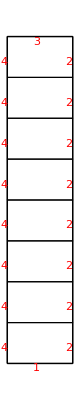

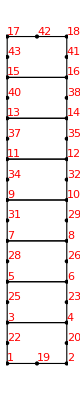

{{0.,0.},{0.1,0.},{0.,0.125},{0.1,0.125},{0.,0.25},{0.1,0.25},{0.,0.375},{0.1,0.375},{0.,0.5},{0.1,0.5},{0.,0.625},{0.1,0.625},{0.,0.75},{0.1,0.75},{0.,0.875},{0.1,0.875},{0.,1.},{0.1,1.},{0.05,0.},{0.1,0.0625},{0.05,0.125},{0.,0.0625},{0.1,0.1875},{0.05,0.25},{0.,0.1875},{0.1,0.3125},{0.05,0.375},{0.,0.3125},{0.1,0.4375},{0.05,0.5},{0.,0.4375},{0.1,0.5625},{0.05,0.625},{0.,0.5625},{0.1,0.6875},{0.05,0.75},{0.,0.6875},{0.1,0.8125},{0.05,0.875},{0.,0.8125},{0.1,0.9375},{0.05,1.},{0.,0.9375}}

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

istep = 5 time = 1.4641 Δt = 0.14641 normresu = 0 normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

istep = 10 time = 2.35795 Δt = 0.235795 normresu = 0 normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

istep = 15 time = 3.7975 Δt = 0.37975 normresu = 0 normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

istep = 20 time = 6.11591 Δt = 0.611591 normresu = 0 normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

istep = 25 time = 9.84973 Δt = 0.984973 normresu = 0 normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

istep = 30 time = 15.8631 Δt = 1.58631 normresu = 0 normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

istep = 35 time = 25.5477 Δt = 2.55477 normresu = 0 normresp = 0

normresu = 1.18903×10^-10

normresp = 0

normresu = 0

normresp = 0

normresu = 1.49927×10^-10

normresp = 0

normresu = 0

normresp = 0

normresu = 1.05667×10^-10

normresp = 0

istep = 40 time = 41.1448 Δt = 4.11448 normresu = 1.05667×10^-10 normresp = 0

normresu = 0

normresp = 0

normresu = 0

normresp = 0

normresu = 1.46625×10^-10

normresp = 0

normresu = 2.96275×10^-10

normresp = 0

normresu = 0

normresp = 0

istep = 45 time = 66.2641 Δt = 6.62641 normresu = 0 normresp = 0

normresu = 4.74913×10^-10

normresp = 0

normresu = 1.05119×10^-10

normresp = 0

normresu = 1.48744×10^-10

normresp = 0

normresu = 2.05908×10^-10

normresp = 0

normresu = 1.61655×10^-10

normresp = 0

istep = 50 time = 106.719 Δt = 10.6719 normresu = 1.61655×10^-10 normresp = 0

normresu = 1.86667×10^-10

normresp = 0

normresu = 1.45883×10^-10

normresp = 0

normresu = 8.58658×10^-10

normresp = 0

normresu = 1.76731×10^-10

normresp = 0

normresu = 5.73343×10^-10

normresp = 0

istep = 55 time = 171.872 Δt = 17.1872 normresu = 5.73343×10^-10 normresp = 0

```mathematica
dim=2; (*Problem Dimension*)
order=2; (*Shape functions order*)
tick=1.;(*Thickness*)
lh=0.1;
lv=1;
tri=False;
If[tri==True,
eltype=TriangleElement;
,
eltype=QuadElement;
];
coordinates={{0,0},{0.1,0.0},{0.1,1.0},{0,1.0}};
boundaryMarker={1,2,3,4};
coordinates={{0,0},{0.1,0.0},{0.1,1.0},{0,1.0}};ele={QuadElement[{{1,2,3,4}}]};boundaryIncidents={{1,2},{2,3},{3,4},{4,1}};
bcEle={LineElement[boundaryIncidents,boundaryMarker]}
(*m=ToElementMesh["Coordinates"->coordinates,"MeshElements"->ele,"BoundaryElements"->bcEle,"NodeReordering"->False]
m=MeshOrderAlteration[m,order];*)

m=SubdivideQuadMesh[coordinates,1,8,boundaryMarker];
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Directive[Red,PointSize[0.1]]]]]
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
meshnodes=m["Coordinates"]

bodyforce={0,0};
young=3 10^5;
nu=0.2;
α=1.;
rhof=1000(*kg/m^3*);
Se=10^-10(*Pa^-1*) ;
mu=10^-2(*Poise= Pascal s *);
perm=10^-10;
dimbc=1;
elasticmaterial=1;
porousmat=2;

bcdata={
{0(*type directional dirichlet*),3(*bcmarker*),{0,1,0}       (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{0(*type directional dirichlet*),2(*bcmarker*),{1,0,0}       (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{0(*type directional dirichlet*),4(*bcmarker*),{1,0,0}       (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{1(*type newman               *),1(*bcmarker*),{0,1000,0}(*force*),                     {0,0,0},dimbc,elasticmaterial},
{0(*type directional dirichlet*),1(*bcmarker*),{0,0,0}     (*pressure*),{0,0,0}(*displacement value*),dimbc,porousmat}
};
bcdata=InsertBCIds[m,bcdata];
{Kglob,Qglob,Hglob,Sglob,Fglob,Fglob2}=Assemble[m,bcdata]//N;

soln1=Table[0,{Length[meshnodes]3}];
un=Table[0,{Length[meshnodes]2}];
pn=Table[0,{Length[meshnodes]}];
plots={};
coordstofind=Table[{lh,0.1},{x,0,lh,0.001}];
idpressure=DeleteDuplicates[Flatten[Table[FindIds[meshnodes,coordstofind[[i]]],{i,1,Length[coordstofind]}]]][[1]];
pressurevstime={};
plotpressure2d={};
plotdisplacement2d={};
displacefuncvec={};
pressurefuncvec={};
pressurevstime={};
(*For[istep=1,istep≤ntimesteps,istep++,*)
time=0.;
scale=1.1;
ntimesteps=55;
(*Δt=1;*)
funcsvec={};
anal={};
For[istep=1,istep≤ntimesteps,istep++,
Δt=scale^istep -time;

{un1,pn1,normresu,normresp}=SolvePoroelastic[m,bcdata,Δt,{un,pn}];
un=un1;
pn=pn1;

If[Divisible[istep,5],
Print["istep = ",istep," time = ",time," Δt = ",Δt, " normresu = ",normresu//Chop, " normresp = ",normresp//Chop];
];

AppendTo[pressurevstime,pn[[idpressure ]]];
If[Divisible[istep,1]||istep==1,


tab=Flatten[Table[Sqrt[ un[[i  2]]^2 +un[[i  2-1]]^2  ],{i, 1,Length[meshnodes] }]];
displacefunc=ElementMeshInterpolation[{m},tab,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
plot=ContourPlot[displacefunc[x,y],{x,0,lh},{y,0,lv},AspectRatio->Automatic];
AppendTo[plotdisplacement2d,plot];

AppendTo[displacefuncvec,displacefunc];

tab=pn;
pressurefunc=ElementMeshInterpolation[{m},tab,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
plot=ContourPlot[pressurefunc[x,y],{x,0,lh},{y,0,lv},AspectRatio->Automatic];
AppendTo[plotpressure2d,plot];

AppendTo[pressurefuncvec,pressurefunc];


ux=Flatten[Table[ un[[i 2-1]]//Chop,{i, 1,Length[meshnodes] }]];
uy=Flatten[Table[ un[[i  2]]//Chop,{i, 1,Length[meshnodes] }]];
uxfunc=ElementMeshInterpolation[{m},ux,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
uyfunc=ElementMeshInterpolation[{m},uy,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
pfunc=ElementMeshInterpolation[{m},pn,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
AppendTo[funcsvec,{uxfunc,uyfunc,pfunc}];

lambda=young nu/((1+nu)(1-2 nu));
G=young/(2 (1+nu));
solp=Sum[2/( Pi/2(2k+1)) Sin[( Pi/2(2k+1)) y/lv]Exp[-(Pi/2(2k+1))^2 (lambda+2 G) perm time/(mu lv^2)],{k,0,10}];
AppendTo[anal,solp];
];
time=scale^istep;

];
```

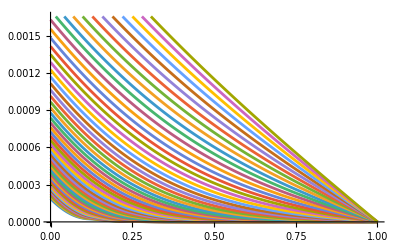

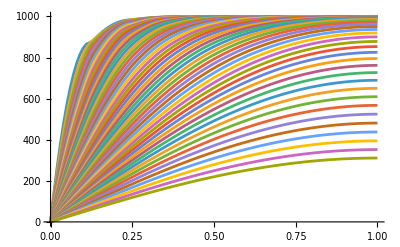

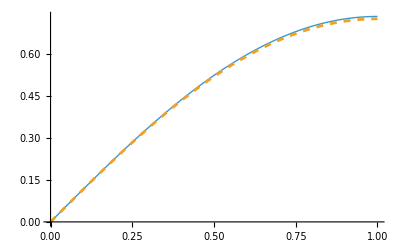

```mathematica
uxvec=Transpose[funcsvec][[1]];
uyvec=Transpose[funcsvec][[2]];
pvec=Transpose[funcsvec][[3]];

plotudata=Table[{y,uyvec[[i]][lh/2,y]},{y,0,lv,0.01},{i,1,Length[displacefuncvec]}];
ListLinePlot[Transpose[plotudata]]
plotpdata=Table[{y,pvec[[i]][lh/2,y]},{y,0,lv,0.01},{i,1,Length[displacefuncvec]}];
ListLinePlot[Transpose[plotpdata],PlotRange->All]
Plot[{anal[[45]],pvec[[45]][lh/2,y]/1000},{y,0,lv},PlotRange->All,PlotStyle->{Thick,Dashed}]
```

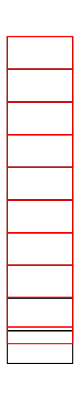

```mathematica
i=2;
ufun=uxvec[[i]];
vfun=uyvec[[i]];
pfun=pvec[[i]];
dmesh=ElementMeshDeformation[m,{ufun,vfun},"ScalingFactor"->300];
Show[{
m["Wireframe"],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}]
(*TableForm[{ContourPlot[pfun[x,y],{x,0,lh},{y,0,lv},AspectRatio->Automatic,PlotLegends->Automatic],
ContourPlot[ufun[x,y],{x,0,lh},{y,0,lv},AspectRatio->Automatic,PlotLegends->Automatic],
ContourPlot[vfun[x,y],{x,0,lh},{y,0,lv},AspectRatio->Automatic,PlotLegends->Automatic]}]*)
```

```mathematica
1000/ 0.1
```

10000.

```mathematica
dim=3; (*Problem Dimension*)
order=2; (*Shape functions order*)
tri=False;
L=10;
b=2;
h=2;
bodyforce={0,0,0};
tetra=False;
If[tetra==True,
eltype=TetrahedronElement;
tri=True;
,
eltype=HexahedronElement;
tri=False;
];
m=ToElementMesh[FullRegion[3],{{0,L},{0,h},{0,b}},"MeshOrder"->order,MaxCellMeasure->L b h/4,"NodeReordering"->True,"MeshElementType"->eltype];
m=MeshOrderAlteration[m,order];
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementMarkerStyle"->Directive[Red,PointSize[0.1]]]]]
Show[m["Wireframe"],m["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
meshnodes=m["Coordinates"];

bodyforce={0,0,0};
young=3 10^5;
nu=0.2;
α=1.;
rhof=1000(*kg/m^3*);
Se=10^-10(*Pa^-1*) ;
mu=10^-2(*Poise= Pascal s *);
perm=10^-10;
dimbc=2;
elasticmaterial=1;
porousmat=2;

bcdata={
{0(*type directional dirichlet*),5(*bcmarker*),{1,0,0}       (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{0(*type directional dirichlet*),3(*bcmarker*),{0,0,1}       (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{0(*type directional dirichlet*),1(*bcmarker*),{0,1,0}       (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{0(*type directional dirichlet*),4(*bcmarker*),{0,0,1}        (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{0(*type directional dirichlet*),2(*bcmarker*),{0,1,0}        (*null direction*),{0,0,0}(*displacement value*),dimbc,elasticmaterial},
{1(*type pressure*),6(*bcmarker*),{-1000(*valuex*),0,0},{0,0}(*direction*),dimbc,elasticmaterial},
{0(*type dirichlet*),6(*bcmarker*),{0(*valuex*),0(*valuey*),0},{0,0}(*direction*),dimbc,porousmat}
};

Δt=0;
bcdata=InsertBCIds[m,bcdata];

soln1=Table[0,{Length[meshnodes]4}];
un=Table[0,{Length[meshnodes]3}];
pn=Table[0,{Length[meshnodes]}];

funcsvec={};

time=0;
scale=1.2;
ntimesteps=20;
Δt=0.00001;
For[istep=1,istep<=ntimesteps,istep++,

Δt=scale^istep -time;

{un1,pn1,normresu,normresp}=SolvePoroelastic[m,bcdata,Δt,{un,pn}];
un=un1;
pn=pn1;
If[Divisible[istep,1],
Print["istep = ",istep," time = ",time," Δt = ",Δt, " normresu = ",normresu//Chop, " normresp = ",normresp//Chop];
];
If[Divisible[istep,1],
ux=Flatten[Table[ un[[i  3-2]]//Chop,{i, 1,Length[meshnodes] }]];
uy=Flatten[Table[ un[[i  3-1]]//Chop,{i, 1,Length[meshnodes] }]];
uz=Flatten[Table[ un[[i  3]]//Chop,{i, 1,Length[meshnodes] }]];
uxfunc=ElementMeshInterpolation[{m},ux,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
uyfunc=ElementMeshInterpolation[{m},uy,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
uzfunc=ElementMeshInterpolation[{m},uz,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
pfunc=ElementMeshInterpolation[{m},pn,"ExtrapolationHandler"->{Function[Indeterminate],"WarningMessage"->False}];
AppendTo[funcsvec,{uxfunc,uyfunc,uzfunc,pfunc}];
];

time=scale^istep;
(*time+=Δt;*)

];
```

-Graphics3D-

-Graphics3D-

istep = 1 time = 0 Δt = 1.2 normresu = 4.77892×10^-7 normresp = 0.0000121386

istep = 2 time = 1.2 Δt = 0.24 normresu = 9.58158×10^-7 normresp = 0.0000465954

istep = 3 time = 1.44 Δt = 0.288 normresu = 8.37974×10^-7 normresp = 0.0000899711

istep = 4 time = 1.728 Δt = 0.3456 normresu = 7.69984×10^-7 normresp = 0.000109569

istep = 5 time = 2.0736 Δt = 0.41472 normresu = 8.78986×10^-7 normresp = 7.70348×10^-6

istep = 6 time = 2.48832 Δt = 0.497664 normresu = 8.17963×10^-7 normresp = 0.0000829757

istep = 7 time = 2.98598 Δt = 0.597197 normresu = 4.51222×10^-7 normresp = 0.0000205888

istep = 8 time = 3.58318 Δt = 0.716636 normresu = 5.6771×10^-7 normresp = 7.52757×10^-6

istep = 9 time = 4.29982 Δt = 0.859963 normresu = 5.82313×10^-7 normresp = 0.0000576828

istep = 10 time = 5.15978 Δt = 1.03196 normresu = 6.82804×10^-7 normresp = 8.90112×10^-6

istep = 11 time = 6.19174 Δt = 1.23835 normresu = 9.11824×10^-7 normresp = 7.50559×10^-6

istep = 12 time = 7.43008 Δt = 1.48602 normresu = 5.81384×10^-7 normresp = 4.1063×10^-6

istep = 13 time = 8.9161 Δt = 1.78322 normresu = 8.73991×10^-7 normresp = 0.0000401821

istep = 14 time = 10.6993 Δt = 2.13986 normresu = 7.88897×10^-7 normresp = 2.86171×10^-6

istep = 15 time = 12.8392 Δt = 2.56784 normresu = 8.19939×10^-7 normresp = 7.73934×10^-6

istep = 16 time = 15.407 Δt = 3.0814 normresu = 5.34296×10^-7 normresp = 2.67648×10^-6

istep = 17 time = 18.4884 Δt = 3.69769 normresu = 6.0384×10^-7 normresp = 6.85472×10^-6

istep = 18 time = 22.1861 Δt = 4.43722 normresu = 4.78555×10^-7 normresp = 6.67535×10^-6

istep = 19 time = 26.6233 Δt = 5.32467 normresu = 5.96151×10^-7 normresp = 3.89458×10^-6

istep = 20 time = 31.948 Δt = 6.3896 normresu = 6.76502×10^-7 normresp = 0.0000220976

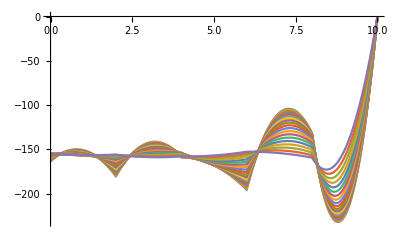

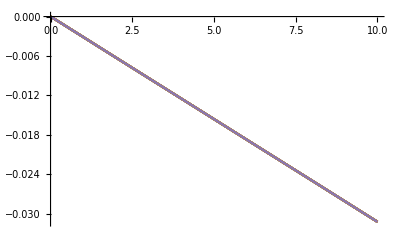

```mathematica
uxvec=Transpose[funcsvec][[1]];
uyvec=Transpose[funcsvec][[2]];
uzvec=Transpose[funcsvec][[3]];
pvec=Transpose[funcsvec][[4]];
plotudata=Table[{x,pvec[[i]][x,b/2,h/2]},{x,0,L,0.01},{i,1,Length[pvec]}];
ListLinePlot[Transpose[plotudata],PlotRange->All]
plotudata=Table[{x,uxvec[[i]][x,b/2,h/2]},{x,0,L,0.01},{i,1,Length[uxvec]}];
ListLinePlot[Transpose[plotudata],PlotRange->All]
```

```mathematica
i=1;
ufun=uxvec[[i]];
vfun=uyvec[[i]];
wfun=uzvec[[i]];
pfun=pvec[[i]];
dmesh=ElementMeshDeformation[m,{ufun,vfun,wfun},"ScalingFactor"->30];
Show[{
m["Wireframe"],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}]
SliceContourPlot3D[pfun[x,y,z],MeshRegion[m],Element[{x,y,z},m],BoxRatios->Automatic,PlotLegends->Automatic]
SliceContourPlot3D[ufun[x,y,z],MeshRegion[m],Element[{x,y,z},m],BoxRatios->Automatic,PlotLegends->Automatic]
SliceContourPlot3D[vfun[x,y,z],MeshRegion[m],Element[{x,y,z},m],BoxRatios->Automatic,PlotLegends->Automatic]
SliceContourPlot3D[wfun[x,y,z],MeshRegion[m],Element[{x,y,z},m],BoxRatios->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

```mathematica
pts=ElementIntegrationPoints[HexahedronElement,order+2]
ws=ElementIntegrationWeights[HexahedronElement,order+2]
```

{{-0.774597,-0.774597,-0.774597},{-0.774597,-0.774597,0.774597},{-0.774597,-0.774597,0.},{-0.774597,0.774597,-0.774597},{-0.774597,0.774597,0.774597},{-0.774597,0.774597,0.},{-0.774597,0.,-0.774597},{-0.774597,0.,0.774597},{-0.774597,0.,0.},{0.774597,-0.774597,-0.774597},{0.774597,-0.774597,0.774597},{0.774597,-0.774597,0.},{0.774597,0.774597,-0.774597},{0.774597,0.774597,0.774597},{0.774597,0.774597,0.},{0.774597,0.,-0.774597},{0.774597,0.,0.774597},{0.774597,0.,0.},{0.,-0.774597,-0.774597},{0.,-0.774597,0.774597},{0.,-0.774597,0.},{0.,0.774597,-0.774597},{0.,0.774597,0.774597},{0.,0.774597,0.},{0.,0.,-0.774597},{0.,0.,0.774597},{0.,0.,0.}}

{0.171468,0.171468,0.274348,0.171468,0.171468,0.274348,0.274348,0.274348,0.438957,0.171468,0.171468,0.274348,0.171468,0.171468,0.274348,0.274348,0.274348,0.438957,0.274348,0.274348,0.438957,0.274348,0.274348,0.438957,0.438957,0.438957,0.702332}

```mathematica
matpsts={{0.7958224257,0.0000000000,0.0000000000,0.8864265927},{-0.7958224257,0.0000000000,0.0000000000,0.8864265927},{0.0000000000,0.7958224257,0.0000000000,0.8864265927},{0.0000000000,-0.7958224257,0.0000000000,0.8864265927},{0.0000000000,0.0000000000,0.7958224257,0.8864265927},{0.0000000000,0.0000000000,-0.7958224257,0.8864265927},{0.7587869106,0.7587869106,0.7587869106,0.3351800554},{0.7587869106,-0.7587869106,0.7587869106,0.3351800554},{0.7587869106,0.7587869106,-0.7587869106,0.3351800554},{0.7587869106,-0.7587869106,-0.7587869106,0.3351800554},{-0.7587869106,0.7587869106,0.7587869106,0.3351800554},{-0.7587869106,-0.7587869106,0.7587869106,0.3351800554},{-0.7587869106,0.7587869106,-0.7587869106,0.3351800554},{-0.7587869106,-0.7587869106,-0.7587869106,0.3351800554}};
```